```mathematica
NS[]
```

```mathematica
assu=(a>0&&a2>0&&b2>0&&s>0&&x∈Reals)
```

a>0&&a2>0&&b2>0&&s>0&&x∈ℝ

```mathematica
ClearAll[mix];mix[a_,a2_,b2_]=Assuming[assu,FS@ParameterMixtureDistribution[GammaDistribution[a,1/rate],{rate\[Distributed]GammaDistribution[a2,1/b2]}]]
```

ParameterMixtureDistribution[GammaDistribution[a,1/rate],rate\[Distributed]GammaDistribution[a2,1/b2]]

```mathematica
tmix[a_,a2_,b2_]=Assuming[assu,FS@TransformedDistribution[-Log[y]/2,y\[Distributed]mix[a,a2,b2]]]
```

TransformedDistribution[-Log[x]/2,x\[Distributed]ParameterMixtureDistribution[GammaDistribution[a,1/rate],rate\[Distributed]GammaDistribution[a2,1/b2]]]

```mathematica
tmix2[shape_,rate_]=Assuming[shape>0&&rate>0,FS@TransformedDistribution[-Log[y]/2,y\[Distributed]GammaDistribution[shape,1/rate]]]
```

TransformedDistribution[-Log[x]/2,x\[Distributed]GammaDistribution[shape,1/rate]]

```mathematica
PDF[tmix[a,a2,b2],x]
```

(2 b2^a2 ⅇ^(-2 a x) (b2+ⅇ^(-2 x))^(-a-a2) Gamma[a+a2])/(Gamma[a] Gamma[a2])

```mathematica
Assuming[assu,FS[PDF[tmix[a,a2,b2],Log[s]+x]-PDF[tmix[a,a2,b2],Log[s]-x]]]
```

(2 b2^a2 ⅇ^(-2 a x) ((b2+ⅇ^(-2 x)/s^2)^(-a-a2) s^(-2 a)-ⅇ^(4 a x) s^(2 a2) (ⅇ^(2 x)+b2 s^2)^(-a-a2)) Gamma[a+a2])/(Gamma[a] Gamma[a2])

```mathematica
Assuming[assu,FS@Series[%,{x,0,3}]]
```

(8 b2^a2 s^(2 a2) (1+b2 s^2)^(-1-a-a2) (a2-a b2 s^2) Gamma[a+a2] x)/(Gamma[a] Gamma[a2])+1/(3 Gamma[a] Gamma[a2])16 b2^a2 s^(2 a2) (1+b2 s^2)^(-3-a-a2) (a2^3-(a+a2+3 a a2+3 (1+a) a2^2) b2 s^2+(a+a2+3 a a2+3 a^2 (1+a2)) b2^2 s^4-a^3 b2^3 s^6) Gamma[a+a2] x^3+O[x]^4

```mathematica
Assuming[assu,FS[Solve[{
(a2-a b2 s^2) ==0,
(a2^3-(a+a2+3 a a2+3 (1+a) a2^2) b2 s^2+(a+a2+3 a a2+3 a^2 (1+a2)) b2^2 s^4-a^3 b2^3 s^6)==0,
a>0,a2>0,b2>0},{a,a2,b2}]]]
```

Solve::svars: Equations may not give solutions for all "solve" variables.

{{a→a2,b2→1/s^2}}

```mathematica
Assuming[assu,FS[PDF[tmix[a,a2,b2],x]/.{b2->1/s^2,a2->a}]]
```

(2 ⅇ^(-2 a x) ((ⅇ^(-2 x)+1/s^2) s)^(-2 a) Gamma[2 a])/Gamma[a]^2

```mathematica
stdtmix=Assuming[assu,StandardDeviation[tmix[a,a,s^2]]/.{s->1/s}]
```

(√PolyGamma[1,a])/(√2)

```mathematica
Assuming[assu,FS@Series[stdtmix,{s,1,1}]]
```

(√PolyGamma[1,a])/(√2)

```mathematica
meantmix=Assuming[assu,Mean[tmix[a,a,1/s^2]]]
```

Log[s]

```mathematica
FindMinimum[{((stdtmix/.{s->10})-Log[10])^2,a>0},{a,1}]
```

{4.9912×10^-16,{a→0.324474}}

```mathematica
FindMinimum[{((stdtmix/.{s->1})-Log[4])^2,a>0},{a,1}]
```

{1.5689×10^-15,{a→0.58016}}

```mathematica
Log[{2,10},a/.%[[2]]]
```

{-0.785477,-0.236452}

```mathematica
(Exp[stdtmix/.{a->#}]&/@{1,1/2,1/3,1/4})//N
```

{2.47663,4.81048,9.45677,18.7717}

```mathematica
(Log[10,Exp[stdtmix/.{a->#}]]&/@{1,1/2,1/4})//N
```

{0.393862,0.682188,1.2735}

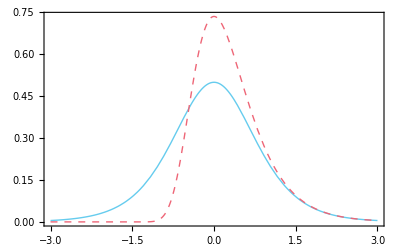

```mathematica
Plot[Evaluate@{PDF[tmix[1,1,1],x],PDF[tmix2[1,1],x]},{x,-3,3},PlotRange->All]
```

```mathematica
Log[10,Exp[2]]//N
```

0.868589

```mathematica
FS[Log[10^x]]
```

Log[10^x]

```mathematica
D[%,x]
```

Log[10]

```mathematica
FS@Log[10,Exp[x]]
```

Log[ⅇ^x]/Log[10]

```mathematica
D[Log[10,Exp[x]],x]
```

1/Log[10]

```mathematica
mean=FS@Mean[TransformedDistribution[1/Identity[y],y\[Distributed]GammaDistribution[shape,1/rate]]]
```

Piecewise[{{rate/(-1+shape), shape>1}, {Indeterminate, True}}]

```mathematica
sd=FS@StandardDeviation[TransformedDistribution[1/Identity[y],y\[Distributed]GammaDistribution[shape,1/rate]]]
```

Piecewise[{{rate/(√(-2+shape) (-1+shape)), shape>2}, {Indeterminate, True}}]

```mathematica
Solve[{mean==m,sd==s,shape>0,rate>0},{shape,rate}]
```

{{shape→ConditionalExpression[(m^2+2 Re[s]^2)/Re[s]^2, (m^2+2 Re[s]^2)/Re[s]^2∈ℝ&&m>0&&s>0],rate→ConditionalExpression[-m+(m (m^2+2 Re[s]^2))/Re[s]^2, (m^2+2 Re[s]^2)/Re[s]^2∈ℝ&&m>0&&s>0]}}

```mathematica
pdf=Assuming[shape>0&&rate>0,FS@PDF[TransformedDistribution[Log[10,1/Sqrt[y]],y\[Distributed]GammaDistribution[shape,1/rate]],x]]
```

(2 ⅇ^(-10^(-2 x) rate) (10^(-2 x) rate)^shape Log[10])/Gamma[shape]

```mathematica
Integrate[pdf*Log[pdf],{x,-Infinity,+Infinity}]
```

$Aborted

```mathematica
{mean=Assuming[shape>0&&rate>0,Simplify@Mean[TransformedDistribution[Log[10,1/Sqrt[y]],y\[Distributed]GammaDistribution[shape,1/rate]]]], sd=Assuming[shape>0&&rate>0,Simplify@StandardDeviation[TransformedDistribution[Log[10,1/Sqrt[y]],y\[Distributed]GammaDistribution[shape,1/rate]]]]}
```

$Aborted

```mathematica
mini=FindMinimum[{(mean-(0))^2+(sd-4)^2,shape>0,rate>0},{{shape,1/10},{rate,1/10}}]
```

FindMinimum::nrnum: The function value -0.374102-0.37142 ⅈ is not a real number at {shape,rate} = {0.0562603,-3.34273×10^-9}.

General::stop: Further output of FindMinimum::nrnum will be suppressed during this calculation.

{1.53814×10^-14,{shape→0.0544091,rate→6.37807×10^-9}}

```mathematica
{mean,sd}/.mini[[2]]
```

{8.15173×10^-8,4.}

General::munfl: Exp[-6370.88] is too small to represent as a normalized machine number; precision may be lost.

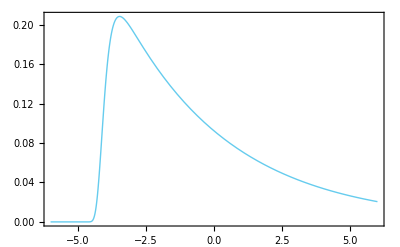

```mathematica
Plot[Evaluate[PDF[TransformedDistribution[Log[10,1/Sqrt[y]],y\[Distributed]GammaDistribution[shape,1/rate]],x]/.mini[[2]]],{x,-6,6},PlotRange->{0,All}]
```

```mathematica
{p1=Assuming[shape>0&&rate>0,FS@InverseCDF[TransformedDistribution[Log[10,1/Sqrt[y]],y\[Distributed]GammaDistribution[shape,1/rate]],5/100]], p2=Assuming[shape>0&&rate>0,FS@InverseCDF[TransformedDistribution[Log[10,1/Sqrt[y]],y\[Distributed]GammaDistribution[shape,1/rate]],95/100]]}
```

{(Log[rate]-Log[InverseGammaRegularized[shape,0,19/20]])/Log[100],(Log[rate]-Log[InverseGammaRegularized[shape,0,1/20]])/Log[100]}

```mathematica
mini2=FindMinimum[{(p1-(-3))^2+(p2-3)^2,shape>0,rate>0},{{shape,1/10},{rate,1/10}},MaxIterations->10000]
```

FindMinimum::nrnum: The function value -0.284135+1.10144 ⅈ is not a real number at {shape,rate} = {0.12587,-0.0000289559}.

General::stop: Further output of FindMinimum::nrnum will be suppressed during this calculation.

FindMinimum::cvmit: Failed to converge to the requested accuracy or precision within 10000 iterations.

{0.187005,{shape→0.118433,rate→4.87019×10^-6}}

```mathematica
{p1,p2}/.mini2[[2]]
```

{-2.5715,2.94177}

General::munfl: Exp[-6370.88] is too small to represent as a normalized machine number; precision may be lost.

General::munfl: Exp[-4.8647×10^6] is too small to represent as a normalized machine number; precision may be lost.

General::munfl: Exp[-4.99436×10^11] is too small to represent as a normalized machine number; precision may be lost.

General::stop: Further output of General::munfl will be suppressed during this calculation.

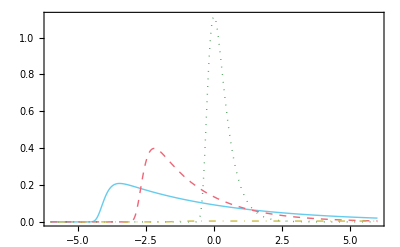

```mathematica
Plot[{Evaluate[PDF[TransformedDistribution[Log[10,1/Sqrt[y]],y\[Distributed]GammaDistribution[shape,1/rate]],x]/.mini[[2]]],Evaluate[PDF[TransformedDistribution[Log[10,1/Sqrt[y]],y\[Distributed]GammaDistribution[shape,1/rate]],x]/.mini2[[2]]],
Evaluate[PDF[TransformedDistribution[Log[10,1/Sqrt[y]],y\[Distributed]GammaDistribution[1/2,2]],x]],
Evaluate[PDF[TransformedDistribution[Log[10,1/Sqrt[y]],y\[Distributed]GammaDistribution[10^-3,10^3]],x]]},{x,-6,6},PlotRange->{-0.01,All}]
```

General::munfl: Exp[-998.872] is too small to represent as a normalized machine number; precision may be lost.

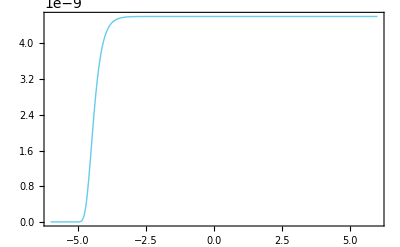

```mathematica
Plot[
Evaluate[PDF[TransformedDistribution[Log[10,1/Sqrt[y]],y\[Distributed]GammaDistribution[10^-9,10^9]],x]],{x,-6,6},PlotRange->{0,All}]
```

General::munfl: Exp[-333145.] is too small to represent as a normalized machine number; precision may be lost.

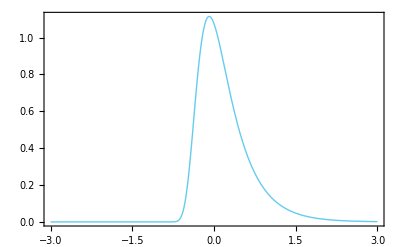

```mathematica
Plot[Evaluate@PDF[TransformedDistribution[Log[10,1/Sqrt[y]],y\[Distributed]GammaDistribution[1/2,2]],x],{x,-3,3},PlotRange->All]
```

```mathematica
pdg[x_,shape_,rate_]=Assuming[shape>0&rate>0&x>0,FS@PDF[GammaDistribution[shape,1/rate],x]]
```

Piecewise[{{(ⅇ^(-rate x) (1/rate)^-shape x^(-1+shape))/Gamma[shape], x>0}, {0, True}}]

```mathematica
pig[x_,shape_,scale_]=Assuming[shape>0&scale>0&x>0,FS@PDF[InverseGammaDistribution[shape,scale],x]]
```

Piecewise[{{(ⅇ^(-scale/x) (scale/x)^shape)/(x Gamma[shape]), x>0}, {0, True}}]

```mathematica
pn[x_,mean_,var_]=Assuming[var>0,FS@PDF[NormalDistribution[mean,Sqrt[var]],x]]
```

(ⅇ^(-(mean-x)^2/(2 var)))/(√(2 π) √var)

```mathematica
pnt[x_,mean_,prec_]=Assuming[prec>0,FS@PDF[NormalDistribution[mean,1/Sqrt[prec]],x]]
```

(ⅇ^(-1/2 prec (mean-x)^2) √prec)/(√(2 π))

```mathematica
combd[x_,scale_]=Assuming[Element[x,Reals]&&scale>0,FS@Integrate[pnt[x,mean,prec]*pnt[mean,0,1/scale^2]*pdg[prec,1/2,1/2*scale^2],{mean,-Infinity,+Infinity},{prec,0,+Infinity}]]
```

1/(2 √2 π^(3/2) scale)ⅇ^((scale-ⅈ x)^2/(2 scale^2)) (-π+π Erfc[(scale-ⅈ x)/(√2 scale)]+ⅇ^((2 ⅈ x)/scale) π Erfc[(scale+ⅈ x)/(√2 scale)]-ⅈ Log[-1/(ⅈ scale+x)]-ⅈ Log[ⅈ scale+x])

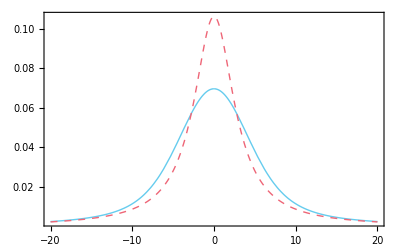

```mathematica
Plot[{combd[x,3],PDF[CauchyDistribution[0,3*1],x]},{x,-20,20},PlotRange->{-0.01,All}]
```

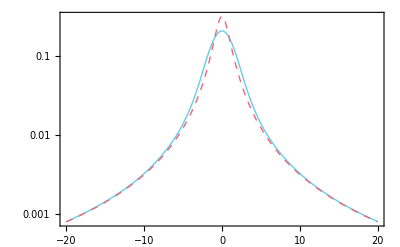

```mathematica
LogPlot[{combd[x,1],PDF[CauchyDistribution[0,1],x]},{x,-20,20},PlotRange->All]
```

```mathematica
ClearAll[combsd];combsd[x_]:=combsd[x]=Assuming[Element[x,Reals],NIntegrate[2*Exp[2*x]*pig[Exp[2*x],shape,rate]*pig[shape,1/2,1/2]*pdg[rate,1/2,1/2],{shape,0,+Infinity},{rate,0,+Infinity},PrecisionGoal->2,MinRecursion->10,MaxRecursion->20]]
```

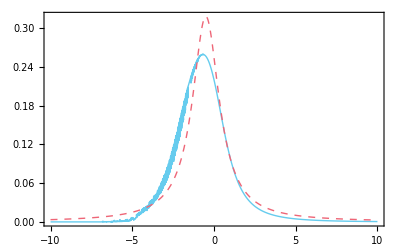

```mathematica
Plot[{combsd[x],PDF[CauchyDistribution[-1/2,1],x]},{x,-10,10},PlotRange->{-0.01,All}]
```

```mathematica
LogPlot[{combsd[x],PDF[CauchyDistribution[-1,2],x]},{x,-10,10},PlotRange->All]
```

NIntegrate::izero: Integral and error estimates are 0 on all integration subregions. Try increasing the value of the MinRecursion option. If value of integral may be 0, specify a finite value for the AccuracyGoal option.

General::stop: Further output of NIntegrate::izero will be suppressed during this calculation.

$Aborted

```mathematica
vard[shape_,rate_]=Assuming[shape>0&&rate>0&&x>0,FS@TransformedDistribution[1/y,y\[Distributed]GammaDistribution[shape,1/rate]]]
```

InverseGammaDistribution[shape,rate]

```mathematica
ClearAll[qvar];qvar[quartile_]=Assuming[shape>0&&rate>0&&0<quartile<1&&x>0,FS@Quantile[vard[shape,rate],quartile]]
```

rate/InverseGammaRegularized[shape,quartile]

```mathematica
meansd=Assuming[shape>0&&rate>0&&x>0,FS@Mean[sdd[shape,rate]]]
```

(√rate Gamma[-1/2+shape])/Gamma[shape]

```mathematica
NMinimize[{(qvar[5/100]-1/100)^2+(qvar[95/100]-100)^2,shape>0,rate>0},{shape,rate},MaxIterations->10000,AccuracyGoal->10,PrecisionGoal->Infinity]
```

{7.03154×10^-12,{shape→0.354295,rate→0.0153473}}

```mathematica
logsdd[shape_,rate_]=Assuming[shape>0&rate>0&x>0,FS@TransformedDistribution[Log[1/Sqrt[y]],y\[Distributed]GammaDistribution[shape,1/rate]]]
```

TransformedDistribution[-Log[x]/2,x\[Distributed]GammaDistribution[shape,1/rate]]

```mathematica
sdd[shape_,rate_]=Assuming[shape>0&&rate>0&&x>0,FS@TransformedDistribution[1/Sqrt[y],y\[Distributed]GammaDistribution[shape,1/rate]]]
```

TransformedDistribution[1/(√x),x\[Distributed]GammaDistribution[shape,1/rate]]

```mathematica
ClearAll[qsd];qsd[quartile_]=Assuming[shape>0&&rate>0&&0<quartile<1&&x>0,FS@Quantile[sdd[shape,rate],quartile]]
```

1/(√(InverseGammaRegularized[shape,0,1-quartile]/rate))

```mathematica
meansd=Assuming[shape>0&&rate>0&&x>0,FS@Mean[sdd[shape,rate]]]
```

(√rate Gamma[-1/2+shape])/Gamma[shape]

```mathematica
NMinimize[{(qsd[10/10]-1/100)^2+(meansd-1)^2,shape>0,rate>0},{shape,rate}]
```

{6.65651×10^-21,{shape→4.56692,rate→3.82503}}

```mathematica
NMinimize[{(qsd[5/100]-1/10)^2+(qsd[95/100]-10)^2,shape>0,rate>0},{shape,rate}]
```

{6.94292×10^-10,{shape→0.354307,rate→0.0153517}}

```mathematica
Mean[sdd[0.35,0.015]]
```

-0.35675

```mathematica
meansd/.%[[2]]
```

-0.374953

```mathematica
psd[x_,shape_,rate_]=Assuming[shape>0&rate>0&x>0,FS@PDF[TransformedDistribution[Log[1/Sqrt[y]],y\[Distributed]GammaDistribution[shape,1/rate]],x]]
```

(2 ⅇ^(-ⅇ^(-2 x) rate-2 shape x) rate^shape)/Gamma[shape]

```mathematica
{Quantile[sdd[0.57,0.015],{1,9.5}/10],Mean[sdd[0.57,0.015]]}//N
```

{{0.100017,1.87454},1.07979}

```mathematica
10
```

```mathematica
{Quantile[sdd[0.51,0.0003],{1,9}/10],Mean[sdd[0.51,0.0003]]}//N
```

{{0.0147756,0.185761},0.990686}

General::munfl: Exp[-7.27153×10^6] is too small to represent as a normalized machine number; precision may be lost.

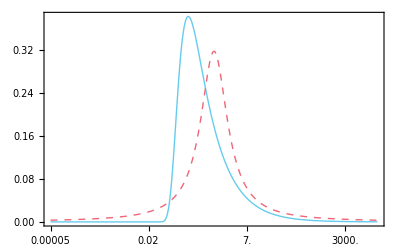

```mathematica
Plot[{psd[x,0.35,0.015],PDF[CauchyDistribution[0,1],x]},{x,-10,10},PlotRange->{-0.01,All},FrameTicks->{Auto,{Table[{i,N[Exp[i],1]},{i,-10,10,2}],None}}]
```

```mathematica
Solve[x*1-5*(1-x)==0,x]
```

{{x→5/6}}

```mathematica
ax=30;meanx=0.75;
NIntegrate[(x*1-(1-x)*5)*PDF[BetaDistribution[ax,ax*(1/meanx-1)],x],{x,5/6,1}]
```

0.0151135

```mathematica
ax=30;meanx=0.85;
NIntegrate[(x*1-(1-x)*5)*PDF[BetaDistribution[ax,ax*(1/meanx-1)],x],{x,5/6,1}]
```

0.201226

```mathematica
casename="case_lowmean_";ax=30;meanx=0.75;plot0=Plot[PDF[BetaDistribution[ax,ax*(1/meanx-1)],x],{x,0,1},PlotRange->{-0.1,6.1},PlotStyle->White,Epilog->{solid,Thickness[Scaled[0.01]],yellow,Line[{{meanx,0},{meanx,7}}]},
FrameLabel->{"frequency of correct predictions",None},FrameTicks->{Auto,None}];
expng[casename<>"1",plot0];
plot1=Plot[PDF[BetaDistribution[ax,ax*(1/meanx-1)],x],{x,0,1},PlotRange->{-0.1,6.1},Epilog->{solid,Thickness[Scaled[0.01]],yellow,Line[{{meanx,0},{meanx,7}}]},
FrameLabel->{"frequency of correct predictions",None},FrameTicks->{Auto,None}];
expng[casename<>"2",plot1];
plot2=Plot[PDF[BetaDistribution[ax,ax*(1/meanx-1)],x],{x,0.833,1},PlotRange->All,Filling->Axis,FillingStyle->green];
expng[casename<>"3",Show[{plot1,plot2}]];
```

```mathematica
casename="case_himean_";ax=30;meanx=0.85;plot0=Plot[PDF[BetaDistribution[ax,ax*(1/meanx-1)],x],{x,0,1},PlotRange->{-0.1,7.1},PlotStyle->White,Epilog->{solid,Thickness[Scaled[0.01]],yellow,Line[{{meanx,0},{meanx,7}}]},
FrameLabel->{"frequency of correct predictions",None},FrameTicks->{Auto,None}];
expng[casename<>"1",plot0];
plot1=Plot[PDF[BetaDistribution[ax,ax*(1/meanx-1)],x],{x,0,1},PlotRange->{-0.1,7.1},Epilog->{solid,Thickness[Scaled[0.01]],yellow,Line[{{meanx,0},{meanx,7}}]},
FrameLabel->{"frequency of correct predictions",None},FrameTicks->{Auto,None}];
expng[casename<>"2",plot1];
plot2=Plot[PDF[BetaDistribution[ax,ax*(1/meanx-1)],x],{x,0,0.833},PlotRange->All,Filling->Axis,FillingStyle->red];
expng[casename<>"3",Show[{plot1,plot2}]];
```

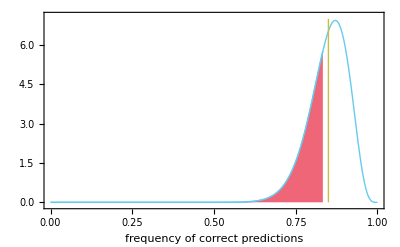

```mathematica
ax=30;meanx=0.85;plot1=Plot[PDF[BetaDistribution[ax,ax*(1/meanx-1)],x],{x,0,1},PlotRange->{-0.1,7.1},Epilog->{solid,Thickness[Scaled[0.01]],yellow,Line[{{meanx,0},{meanx,7}}]},
FrameLabel->{"frequency of correct predictions",None},FrameTicks->{Auto,None}];
plot2=Plot[PDF[BetaDistribution[ax,ax*(1/meanx-1)],x],{x,0,0.833},PlotRange->All,Filling->Axis,FillingStyle->red];
Show[{plot1,plot2}]
```

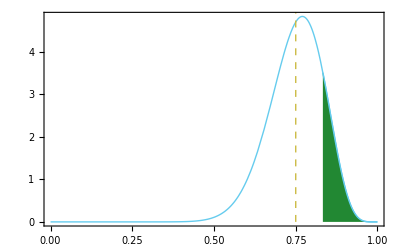

```mathematica
ax=20;meanx=0.75;plot1=Plot[PDF[BetaDistribution[ax,ax*(1/meanx-1)],x],{x,0,1},PlotRange->All,Epilog->{Dashed,Thick,yellow,Line[{{meanx,0},{meanx,6}}]}];
plot2=Plot[PDF[BetaDistribution[ax,ax*(1/meanx-1)],x],{x,0.833,1},PlotRange->All,Filling->Axis,FillingStyle->green];
Show[{plot1,plot2}]
```

```mathematica
ax=20;plot1=Plot[PDF[BetaDistribution[ax,ax*(1/0.75-1)],x],{x,0,1},PlotRange->All,Epilog->{Dashed,Thick,Line[{{0.75,0},{0.75,5}}]}];
plot2=Plot[PDF[BetaDistribution[ax,ax*(1/0.75-1)],x],{x,0.833,1},PlotRange->All,Filling->Axis,FillingStyle->green];
Show[{plot1,plot2}]
```

```mathematica
FS@Solve[{Mean[BetaDistribution[a,b]]==m,StandardDeviation[BetaDistribution[a,b]]==s},{a,s}]
```

Solve::nongen: Solutions may not be valid for all values of parameters.

{{a→-(b m)/(-1+m),s→-(ⅈ (-1+m) √m)/(√(-1-b+m))},{a→-(b m)/(-1+m),s→(ⅈ (-1+m) √m)/(√(-1-b+m))}}

```mathematica
FS@Solve[{Mean[BetaDistribution[a,b]]==m},{b,m}]
```

Solve::svars: Equations may not give solutions for all "solve" variables.

{{b→a (-1+1/m)}}

```mathematica
Mean[TransformedDistribution[1/ia,ia\[Distributed]GammaDistribution[1/2,1/2/m]]]
```

Indeterminate

```mathematica
newgd[a_,m_]=GammaDistribution[a/2,2*m/a]
```

GammaDistribution[a/2,(2 m)/a]

```mathematica
PDF[newgd[1,1],x]
```

Piecewise[{{ⅇ^(-x/2)/(√(2 π) √x), x>0}, {0, True}}]

```mathematica
Mean[newgd[a,m]]
```

m

```mathematica
TransformedDistribution[a/k,a\[Distributed]InverseGammaDistribution[1/2,1/2]]
```

InverseGammaDistribution[1/2,1/(2 k)]

```mathematica
TransformedDistribution[1/ia,ia\[Distributed]GammaDistribution[1/2,2*m]]
```

InverseGammaDistribution[1/2,1/(2 m)]

```mathematica
trd[x_]=PDF[TransformedDistribution[Log[v],v\[Distributed]GammaDistribution[1/2,2]],x]
```

(ⅇ^(1/2 (-ⅇ^x+x)))/(√(2 π))

```mathematica
trid[x_]=PDF[TransformedDistribution[Log[v],v\[Distributed]InverseGammaDistribution[1/2,1/2*10]],x]
```

ⅇ^(-5 ⅇ^-x-x/2) √(5/π)

General::munfl: Exp[-739.414] is too small to represent as a normalized machine number; precision may be lost.

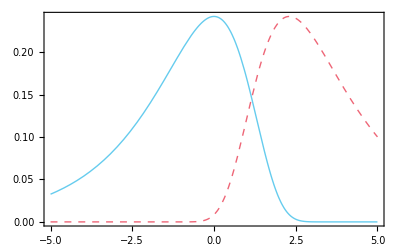

```mathematica
Plot[{trd[x],trid[x]},{x,-5,5}]
```

```mathematica
cd=TransformedDistribution[(q1*m1+q2*m2+q3*m3)/(q1+q2+q3),{q1\[Distributed]GammaDistribution[a,1],q2\[Distributed]GammaDistribution[a,1],q3\[Distributed]GammaDistribution[a,1],m1\[Distributed]NormalDistribution[m,s],m2\[Distributed]NormalDistribution[m,s],m3\[Distributed]NormalDistribution[m,s]}]
```

TransformedDistribution[(x1 x4+x2 x5+x3 x6)/(x1+x2+x3),{x1\[Distributed]GammaDistribution[a,1],x2\[Distributed]GammaDistribution[a,1],x3\[Distributed]GammaDistribution[a,1],x4\[Distributed]NormalDistribution[m,s],x5\[Distributed]NormalDistribution[m,s],x6\[Distributed]NormalDistribution[m,s]}]

```mathematica
Mean[cd]
```

m

```mathematica
Variance[cd]
```

Variance[TransformedDistribution[(x1 x4+x2 x5+x3 x6)/(x1+x2+x3),{x1\[Distributed]GammaDistribution[a,1],x2\[Distributed]GammaDistribution[a,1],x3\[Distributed]GammaDistribution[a,1],x4\[Distributed]NormalDistribution[m,s],x5\[Distributed]NormalDistribution[m,s],x6\[Distributed]NormalDistribution[m,s]}]]

```mathematica
Variance[cd]
```

((1+a) s^2)/(1+2 a)

```mathematica
cd2=TransformedDistribution[{q1,q2,1-q1-q2}.{m1,m2,m3},{{q1,q2}\[Distributed]DirichletDistribution[{a,a,a}/3],m1\[Distributed]NormalDistribution[m,s],m2\[Distributed]NormalDistribution[m,s],m3\[Distributed]NormalDistribution[m,s],m4\[Distributed]NormalDistribution[m,s]}]
```

TransformedDistribution[m1 q1+m3 (1-q1-q2)+m2 q2,{q1,q2,m1,m2,m3}\[Distributed]ProductDistribution[DirichletDistribution[{a/3,a/3,a/3}],NormalDistribution[m,s],NormalDistribution[m,s],NormalDistribution[m,s]]]

```mathematica
Mean[cd2]
```

m

```mathematica
FS@Variance[cd2]
```

((3+a) s^2)/(3 (1+a))

```mathematica
cd2=TransformedDistribution[{q1,q2,q3,1-q1-q2-q3}.{m1,m2,m3,m4},{{q1,q2,q3}\[Distributed]DirichletDistribution[{a,a,a,a}],m1\[Distributed]NormalDistribution[m,s],m2\[Distributed]NormalDistribution[m,s],m3\[Distributed]NormalDistribution[m,s],m4\[Distributed]NormalDistribution[m,s]}]
```

TransformedDistribution[m1 q1+m2 q2+m4 (1-q1-q2-q3)+m3 q3,{{q1,q2,q3}\[Distributed]DirichletDistribution[{a,a,a,a}],m1\[Distributed]NormalDistribution[m,s],m2\[Distributed]NormalDistribution[m,s],m3\[Distributed]NormalDistribution[m,s],m4\[Distributed]NormalDistribution[m,s]}]

```mathematica
Mean[cd2]
```

m

```mathematica
FS@Variance[cd2]
```

((1+a) s^2)/(1+4 a)

```mathematica
ad2=TransformedDistribution[{q1,q2,1-q1-q2}.{s1,s2,s3},{{q1,q2}\[Distributed]DirichletDistribution[{a,a,a}],
s1\[Distributed]InverseGammaDistribution[t1,t2],
s2\[Distributed]InverseGammaDistribution[t1,t2],
s3\[Distributed]InverseGammaDistribution[t1,t2]}]
```

TransformedDistribution[q1 s1+q2 s2+(1-q1-q2) s3,{{q1,q2}\[Distributed]DirichletDistribution[{a,a,a}],s1\[Distributed]InverseGammaDistribution[t1,t2],s2\[Distributed]InverseGammaDistribution[t1,t2],s3\[Distributed]InverseGammaDistribution[t1,t2]}]

```mathematica
FS@Mean[ad2]
```

Mean[TransformedDistribution[q1 s1+q2 s2+s3-(q1+q2) s3,{{q1,q2}\[Distributed]DirichletDistribution[{a,a,a}],s1\[Distributed]InverseGammaDistribution[t1,t2],s2\[Distributed]InverseGammaDistribution[t1,t2],s3\[Distributed]InverseGammaDistribution[t1,t2]}]]

```mathematica
ad2=TransformedDistribution[{q1,q2,1-q1-q2}.{s1+m1^2,s2+m2^2,s3+m3^2},{{q1,q2}\[Distributed]DirichletDistribution[{a,a,a}],m1\[Distributed]NormalDistribution[m,s],m2\[Distributed]NormalDistribution[m,s],m3\[Distributed]NormalDistribution[m,s],m4\[Distributed]NormalDistribution[m,s],
s1\[Distributed]InverseGammaDistribution[t1,t2],
s2\[Distributed]InverseGammaDistribution[t1,t2],
s3\[Distributed]InverseGammaDistribution[t1,t2],
s4\[Distributed]InverseGammaDistribution[t1,t2]}]
```

TransformedDistribution[x1 (x3^2+x6)+x2 (x4^2+x7)+(1-x1-x2) (x5^2+x8),{x1,x2,x3,x4,x5,x6,x7,x8}\[Distributed]ProductDistribution[DirichletDistribution[{a,a,a}],NormalDistribution[m,s],NormalDistribution[m,s],NormalDistribution[m,s],InverseGammaDistribution[t1,t2],InverseGammaDistribution[t1,t2],InverseGammaDistribution[t1,t2]]]

```mathematica
ad2=TransformedDistribution[{q1,q2,q3,1-q1-q2-q3}.{s1+m1^2,s2+m2^2,s3+m3^2,s4+m4^2}-({q1,q2,q3,1-q1-q2-q3}.{m1,m2,m3,m4})^2,{{q1,q2,q3}\[Distributed]DirichletDistribution[{1,1,1,1}/4],m1\[Distributed]NormalDistribution[0,3],m2\[Distributed]NormalDistribution[0,3],m3\[Distributed]NormalDistribution[0,3],m4\[Distributed]NormalDistribution[0,3],
s1\[Distributed]InverseGammaDistribution[t1,t2],
s2\[Distributed]InverseGammaDistribution[t1,t2],
s3\[Distributed]InverseGammaDistribution[t1,t2],
s4\[Distributed]InverseGammaDistribution[t1,t2]}]
```

TransformedDistribution[-(m1 q1+m2 q2+m4 (1-q1-q2-q3)+m3 q3)^2+q1 (m1^2+s1)+q2 (m2^2+s2)+q3 (m3^2+s3)+(1-q1-q2-q3) (m4^2+s4),{{q1,q2,q3}\[Distributed]DirichletDistribution[{1/4,1/4,1/4,1/4}],m1\[Distributed]NormalDistribution[0,3],m2\[Distributed]NormalDistribution[0,3],m3\[Distributed]NormalDistribution[0,3],m4\[Distributed]NormalDistribution[0,3],s1\[Distributed]InverseGammaDistribution[t1,t2],s2\[Distributed]InverseGammaDistribution[t1,t2],s3\[Distributed]InverseGammaDistribution[t1,t2],s4\[Distributed]InverseGammaDistribution[t1,t2]}]

```mathematica
mean=FS@Mean[ad2]
```

Mean[TransformedDistribution[-(m1 q1+m2 q2+m3 q3-m4 (-1+q1+q2+q3))^2+q1 (m1^2+s1)+q2 (m2^2+s2)+q3 (m3^2+s3)-(-1+q1+q2+q3) (m4^2+s4),{{q1,q2,q3}\[Distributed]DirichletDistribution[{1/4,1/4,1/4,1/4}],m1\[Distributed]NormalDistribution[0,3],m2\[Distributed]NormalDistribution[0,3],m3\[Distributed]NormalDistribution[0,3],m4\[Distributed]NormalDistribution[0,3],s1\[Distributed]InverseGammaDistribution[t1,t2],s2\[Distributed]InverseGammaDistribution[t1,t2],s3\[Distributed]InverseGammaDistribution[t1,t2],s4\[Distributed]InverseGammaDistribution[t1,t2]}]]

```mathematica
Plot3D[mean,{t1,0,10},{t2,0,10},PlotPoints->32]
```

$Aborted

```mathematica
FS@Mean[ad2]
```

Mean[TransformedDistribution[x1 (x3^2+x6)+x2 (x4^2+x7)-(-1+x1+x2) (x5^2+x8),{x1,x2,x3,x4,x5,x6,x7,x8}\[Distributed]ProductDistribution[DirichletDistribution[{a,a,a}],NormalDistribution[m,s],NormalDistribution[m,s],NormalDistribution[m,s],InverseGammaDistribution[t1,t2],InverseGammaDistribution[t1,t2],InverseGammaDistribution[t1,t2]]]]

```mathematica
FS@Variance[ad2]
```

(q1^2+q2^2+q3^2+(-1+q1+q2+q3)^2) s^2

```mathematica
meanr[q1_,q2_,q3_,m_,s_,t1_,t2_]:=
```

```mathematica
mumix=ParameterMixtureDistribution[ProductDistribution[NormalDistribution[mu,s1],NormalDistribution[mu,s1]],mu\[Distributed]NormalDistribution[0,s0]]
```

ParameterMixtureDistribution[ProductDistribution[NormalDistribution[mu,s1],NormalDistribution[mu,s1]],mu\[Distributed]NormalDistribution[0,s0]]

```mathematica
FS@PDF[mumix,{x,y}]
```

(ⅇ^(-(s0^2 (x-y)^2+s1^2 (x^2+y^2))/(2 s1^2 (2 s0^2+s1^2))))/(2 π s0 √(1/s0^2+2/s1^2) s1^2)

```mathematica
Covariance[mumix]//MF
```

(s0^2+s1^2 | s0^2
s0^2 | s0^2+s1^2)